```mathematica
Get["invariant_dmd_v2_8_functions"];
Get["invariant_dmd_v2_8_auxuntested_v1"];
```

```mathematica
Get["dslibrary_v3_3"];
```

## Savefile

```mathematica
savefile = "manyfp2Deg1_pruned_v1";
```

## Temporal parameters

0 usually - If delayed, set appropriately

```mathematica
ndelays = 0;

tinit = 0;
tsamp = 0.2;
```

#### Choice of DS

```mathematica
(* Create a separate one for each DS*)
vfield = manyfp2Deg1;
(* Did not know a better way to do ICs without distrubing the code that follows *)

(* chosenputty: Use to convert coordinates from the ODE version *)
chosenputty = #& ;
```

### Tolerances

```mathematica
(* Tolerance *)
sigtols = {10^-8,10^-12}; (* Singular values *)
restols = {10^-8,10^-12};(* greaterabsrelcheck *)
```

### Flavours

Switches for the constant eigenfunction && the delay constraints (You need to put the constant function in userhead !!!) : Set True to activate

#### User defined functions

```mathematica
(* AppendTo[userlist,(*Desired fheads*)];*)
userparams = {};
```

#### User defined constraints

Should be a LIST of matrices !!!

```mathematica
(* Geometric constraints *)
invsamplesets ;
(* Functional constraints *)
ipfuns(**);
opfuns(**);
rawuserlist = {};
```

#### Test constraints

```mathematica
testinvsamplesets=N@invsets4manyfp2Deg1;
testipfuns;
testopfuns;
```

```mathematica
boxranges = {{-1,1},{-1,1}};
centercounts = {{37,37},{11,11}(* Must be the same as the first to ensure that the scaling is correctly done for trigtri *)};
nsampsperbox = {3,3};
flavour = "boxfuns";


(* How muich of the fringe be included in the plots*)
plotscalefactor = 1.1;
```

## Must use this version !!!!

```mathematica
icsconwrap4modifiedoneshot[ics_,{{construct_,basistruct_,invsamplesets_,testinvsamplesets_},{userparams_,rawuserlist_,ipfuns_,opfuns_,testipfuns_,testopfuns_}}]:=modifiedoneshot[ndelays,tinit,tsamp,vfield,ics,chosenputty,sigtols,restols,flavour,flavourparams,construct,basistruct,userparams,rawuserlist,invsamplesets,ipfuns,opfuns,testinvsamplesets,testipfuns,testopfuns,boxflavourparams];
```

## Actual test

#### Sample points

```mathematica
boxflavourparams = {boxranges,centercounts[[-1]]};
flavourparams ={boxranges,centercounts[[1]]};
```

```mathematica
detics = N@Join@@MapThread[(#1@(getdetseeds4Box[boxranges,#2,#3]))&,{{#&,puttheseoutright[#,boxflavourparams]&},centercounts,nsampsperbox}];
ncompsamples = Length@detics;
```

#### Plot points

```mathematica
plotcc = centercounts[[1]];
plotspb = nsampsperbox[[1]];
plotbrs  = plotscalefactor *boxranges;
plotparams = {plotbrs,plotcc,plotspb};
(*----------ODE in sampled coordinates ----------*)
plotics = N@getdetseeds4Box@@plotparams;
```

### Le test variations

#### Expected spectrum

```mathematica
jacobevals =FunctionExpand@Flatten@Map[N@Eigenvalues@getjacobian[(*Vector field *)vfield,{t,#}]&,(*fixedpoints*)Flatten[testinvsamplesets,1]];
expectedevalues  = Exp[jacobevals*tsamp];
```

```mathematica
neededbaggage = {detics,plotics,sigtols,tsamp,ncompsamples,ndelays,flavourparams,expectedevalues};
```

```mathematica
activecons;
passivecons = {userparams,rawuserlist,ipfuns,opfuns,testipfuns,testopfuns};
```

```mathematica
Print[{centercounts,nsampsperbox}];
goodplotgrub=MapThread[getcrunchedata[{#1,#2,#3,testinvsamplesets},passivecons,neededbaggage]&,{{True,True,False},{True,True,False},{testinvsamplesets,{},{}}}];
DumpSave[savefile,{goodplotgrub,plotparams}];
Quit[];
```

{{{37,37},{11,11}},{3,3}}

{0.2,13345,0,{{{-1,1},{-1,1}},{37,37}},{9.21585,0},{{2.19837×10^-15,9.70774×10^-14},{6.90615×10^-15,6.90615×10^-15}},1258.4}

{0.2,13345,0,{{{-1,1},{-1,1}},{37,37}},{9.30281,0},{{0.960769,30.5941},{1.3253×10^-15,1.3253×10^-15}},1255.05}

{0.2,13345,0,{{{-1,1},{-1,1}},{37,37}},{1.,0},{{0.963624,30.5941},{}},1255.05}

### Plots

```mathematica
(* Also fetch all functions in auxuntested_v1 *)
Get["invariant_dmd_v2_8_functions"];
Get["invariant_dmd_v2_8_auxuntested_v1"];
(* Typically file name is stored in savefile *)
Get["manyfp2Deg1_pruned_v1"];
```

Pass 1

Pass 2

Pass 3

Pass 4

Pass 5

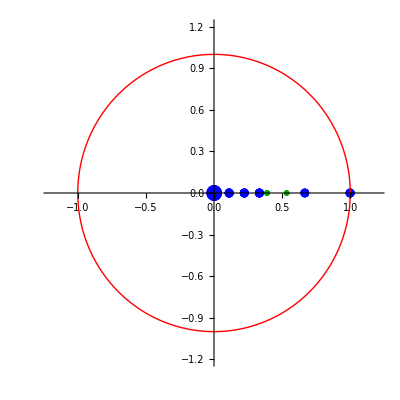
{-Graphics-,-Graphics-}

-Graphics-

```mathematica
visualizespectrum [goodplotgrub[[1]],plotparams];
```

```mathematica
plotics = N@getdetseeds4Box@@plotparams;
```

```mathematica
{ploticslifted,testefgrubvecs} = goodplotgrub[[1,{2,3}]];
```

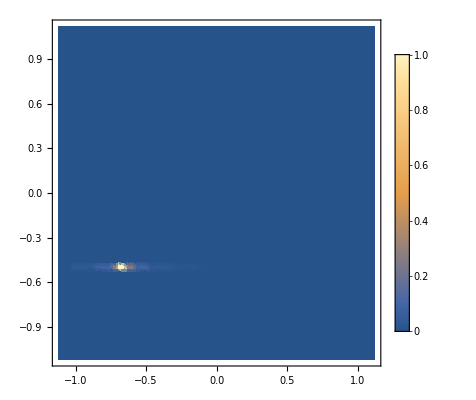
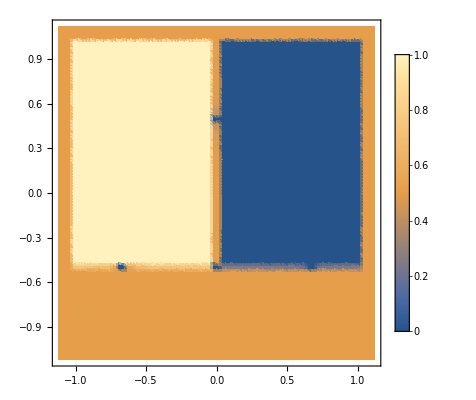
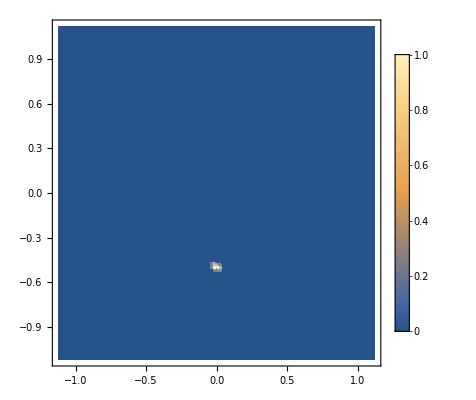
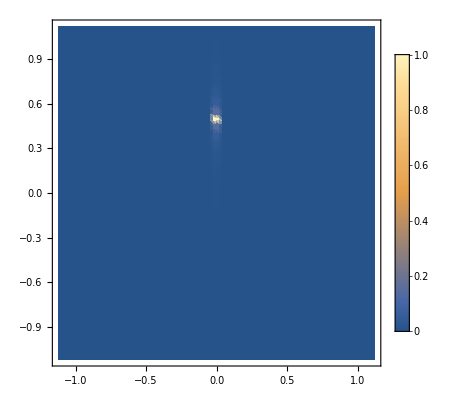
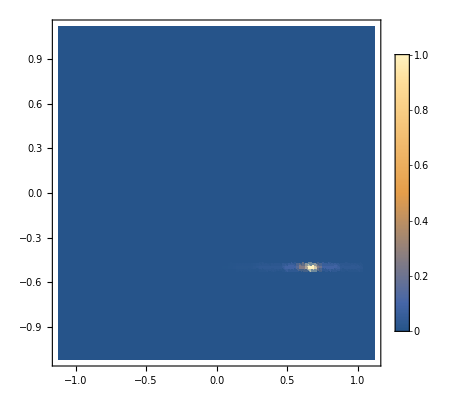
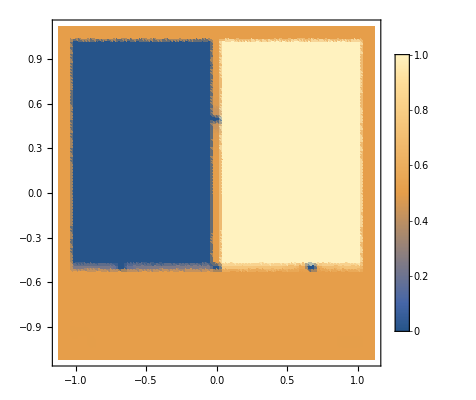

```mathematica
Table[ListDensityPlot[getlistplotdata[testefgrubvecs[[i,1]],N@plotics,ploticslifted,Abs],PlotRange->All,PerformanceGoal->"Quality",PlotLegends->Automatic,LabelStyle->Directive[Black, Medium]],{i,6}]
```